```mathematica
(*Symmetric Confined Vortex Surface By Minimization *)
WW =DiagonalMatrix[{a,b,-a-b}];
NN[θ_,φ_] = {Sin[θ]Cos[φ], Sin[θ]Sin[φ], Cos[θ]};
DN[θ_,φ_] = D[NN[θ,φ],φ]
{-Sin[θ] Sin[φ],Cos[φ] Sin[θ],0}
II = NN[θ,φ].WW.Cross[NN[θ,φ],DN[θ,φ]]//Simplify
```

{-Sin[θ] Sin[φ],Cos[φ] Sin[θ],0}

{-Sin[θ] Sin[φ],Cos[φ] Sin[θ],0}

-1/2 Cos[θ] (3 (a+b)+(a-b) Cos[2 φ]) Sin[θ]^2

```mathematica
-1/2 Cos[θ] (3 (a+b)+(a-b) Cos[2 φ]) Sin[θ]^2
DPL[l_,z_] =D[LegendreP[l,z],z];
```

-1/2 Cos[θ] (3 (a+b)+(a-b) Cos[2 φ]) Sin[θ]^2

```mathematica
III[u_,v_] = Assuming[{u > v, v> 0},Integrate[Cos[x]/Sqrt[u - v Cos[x]],{x,0,2 Pi}]]//Simplify
```

1/(v √(u^2-v^2))2 ((-u+v) √(u+v) EllipticE[-(2 v)/(u-v)]-√(u-v) (u+v) EllipticE[(2 v)/(u+v)]+u (√(u+v) EllipticK[-(2 v)/(u-v)]+√(u-v) EllipticK[(2 v)/(u+v)]))

```mathematica
eps = 10^(-10);
```

```mathematica
IC[z1_, z2_]:= With [
{u =eps +2-2  z1 z2,
v = 2 Sqrt[(1-z1^2)(1-z2^2)]},
 Sqrt[(1-z1^2)(1-z2^2)]/4III[u,v] ];
```

```mathematica
CompiledIC=Compile[
{z1,z2},
IC[z1,z2],
"RuntimeOptions"->"EvaluateSymbolically"->False
];
```

```mathematica
CompiledIC[0.4,0.5]
```

0.964098

```mathematica
Hmat[n_, m_] :=2NIntegrate[
Hold@With[
{z2 =2 t2 -1},
DPL[m,z2]
With[
{z1 = 2 t2 t -1},
DPL[n,z1]  CompiledIC[ z1,z2]]
],{t,0.,1.},{t2,0.,1.},Method->"LocalAdaptive"];
```

```mathematica
Hmat[2,2]
```

1.47257

```mathematica
Hmat[3,5]
```

0.858907

```mathematica
L = 20;
```

```mathematica
TT =ParallelTable[Hmat[n,m],{n,L},{m,L}];
MM = (TT + Transpose[TT])/2;
```

```mathematica
Export["MM.wdx",MM];
```

$Aborted

```mathematica
II[z_]= -3 z (1-z^2)
```

-3 z (1-z^2)

```mathematica
Bvec[l_]:= 2 Pi Integrate[ -DPL[l,z]  II[z],{z,-1,1}];
```

```mathematica
BB =-Table[ Bvec[n], {n,L}]
```

```mathematica
GG = γ /@ Range[L]
```

```mathematica
SolG =Solve[MM.GG== BB ,GG][[1]];
```

```mathematica
Export["GGslashdotSolG.csv",GG/.SolG]
```

{-9.29397,-20.5052,-9.45229,-0.423481,-0.0240043,-0.0217554,-0.00311002,-0.00413707,-0.000776786,-0.00148783}

```mathematica
GammaFunc[z_] := Sum[γ[l] (LegendreP[l,z]-LegendreP[l,1]),{l,0,L}];
```

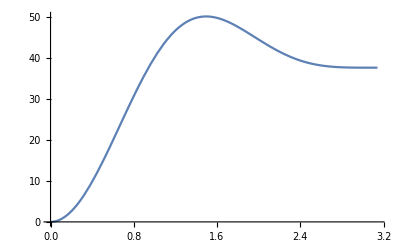

```mathematica
Plot[GammaFunc[Cos[θ]],{θ,0,Pi}]
```